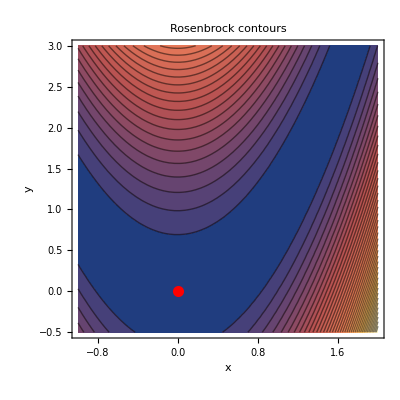

{0.0504262,{x→1.22437,y→1.5}}

```mathematica
(* ::Package::*)(*1 ── Define the objective and visual check*)
ClearAll[f,x,y];
f[x_,y_]:=(1-x)^2+100 (y-x^2)^2;

ContourPlot[f[x,y],{x,-1,2},{y,-0.5,3},PlotRange->All,Contours->40,Epilog->{Red,PointSize[0.02],Point[{0,0}]},FrameLabel->{"x","y"},PlotLabel->"Rosenbrock contours"]

(*2 ── Bounded nonlinear optimisation*)
bounds={x>=0,y>=1.5};

(*interior-point Newton with a tight gradient tolerance*)
solution=FindMinimum[{f[x,y],bounds},{x,y},Method->{"InteriorPoint","Tolerance"->1.*^-8},AccuracyGoal->10,PrecisionGoal->10]
```

```mathematica
(*3 ── Extract results*)
{fmin,rules}=solution;
{xOpt,yOpt}={x,y}/. rules//N[#,20]&
```

{1.22437,1.5}

```mathematica
Print["f*    = ",NumberForm[fmin,20]];
Print["x*,y* = ",{NumberForm[xOpt,10],yOpt}];
```

f*    = 0.05042618789360759

x*,y* = {1.224370749,1.5}

```mathematica
Print["Minimum value   f* = ",fmin//N];
Print["Optimal point   x* = ",xOpt,",  y* = ",yOpt];

(*4 ── Verify the projected-gradient stop test||P[x-∇f]-x||∞*)
grad=Grad[f[x,y],{x,y}]/. rules//N
```

Minimum value   f* = 0.0504262

Optimal point   x* = 1.22437,  y* = 1.5

{1.3216×10^-11,0.183254}

```mathematica
proj=MapThread[Max,{bounds[[All,2]],{xOpt,yOpt}-grad}]
```

{1.22437,1.5}

```mathematica
{xOpt,yOpt}-grad
```

{1.22437,1.31675}

```mathematica
Abs[proj-{xOpt,yOpt}]
```

{1.32159×10^-11,2.66454×10^-15}

```mathematica
projGap=Max@Abs[proj-{xOpt,yOpt}];

Print["Projected-gradient ∞-norm = ",projGap];
```

Projected-gradient ∞-norm = 1.32159×10^-11

```mathematica
Grad[f[x,y],{x,y}]/.{x->2.97495 ,y->1.5}
```

{8750.69,-1470.07}

```mathematica
rules
```

{x→1.22437,y→1.5}